```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* Read the data file and reshape it *)
```

```mathematica
ncol=6;c=0.7614;
data=ReadList["/home/romaingrvl/MEGAsync/thèse/freefem/spinning_mini_BS/data/mathematica/bs_mat_om=0.9_m=1_c=0.7614.out",Number];
data=data/.$Failed->0;
nline=Length[data]/ncol;
datashaped=ArrayReshape[data,{nline,ncol}]
```

```mathematica
(* Check the values of the grid bounds *)
```

```mathematica
xmin=Min[datashaped[[All,1]]]
xmax=Max[datashaped[[All,1]]]
θmin=Min[datashaped[[All,2]]]
θmax=Max[datashaped[[All,2]]]
```

0

1

0

1.5708

```mathematica
(* Useful things for later *)
```

```mathematica
R[x_]:=c x/(1-x);
```

```mathematica
(* Construct tabulated values of the scalar field in compactified coordinates and interpolate *)
```

```mathematica
dataϕ=Table[{{datashaped[[i,1]],datashaped[[i,2]]},datashaped[[i,3]]},{i,nline}];
```

```mathematica
(* ϕ: scalar field profile in compactified coordinates 
ϕρz: scalar field profile in cylindrical coordinates *)
```

```mathematica
ϕ=Interpolation[dataϕ,InterpolationOrder->3]
ϕρz[ρ_,z_]:=ϕ[Sqrt[ρ^2+z^2]/(Sqrt[ρ^2+z^2]+c),ArcTan[Abs[z],ρ]]
```

InterpolatingFunction[…]

```mathematica
Plot3D[ϕ[x,θ],{x,xmin,xmax},{θ,θmin,θmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
ρmax=0.5;zmax=ρmax/2;
Plot3D[ϕρz[ρ,z],{ρ,0,ρmax},{z,-zmax,zmax},PlotPoints->100,PlotRange->All,Mesh->None,BoundaryStyle->None,ColorFunction->ColorData[{"SunsetColors",{1.1,-0.5}}]]
```

-Graphics3D-

```mathematica
θmax
```

1.5708

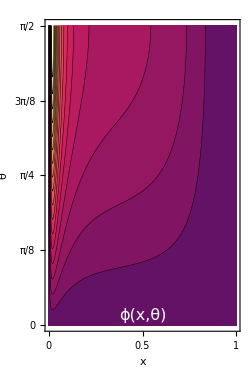

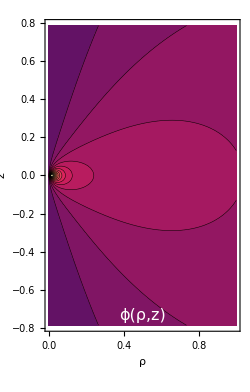

```mathematica
ρmax=1;zmax=ρmax/2*(θmax/xmax);
customticks={{{{0,"0",0.01},{π/32,"",0.005},{π/16,"",0.005},{3π/32,"",0.005},{π/8,"π/8",0.01},{5π/32,"",0.005},{3π/16,"",0.005},{7π/32,"",0.005},{π/4,"π/4",0.01},{9π/32,"",0.005},{5π/16,"",0.005},{11π/32,"",0.005},{3π/8,"3π/8",0.01},{13π/32,"",0.005},{7π/16,"",0.005},{15π/32,"",0.005},{1.57079632679,"π/2",0.01}},{{0,"",0.01},{π/32,"",0.005},{π/16,"",0.005},{3π/32,"",0.005},{π/8,"",0.01},{5π/32,"",0.005},{3π/16,"",0.005},{7π/32,"",0.005},{π/4,"",0.01},{9π/32,"",0.005},{5π/16,"",0.005},{11π/32,"",0.005},{3π/8,"",0.01},{13π/32,"",0.005},{7π/16,"",0.005},{15π/32,"",0.005},{1.57079632679,"",0.01}}}, {{0,{0.0625,"",0.005},{2*0.0625,"",0.005},{3*0.0625,"",0.005},0.25,{5*0.0625,"",0.005},{6*0.0625,"",0.005},{7*0.0625,"",0.005},0.5,{9*0.0625,"",0.005},{10*0.0625,"",0.005},{11*0.0625,"",0.005},0.75,{13*0.0625,"",0.005},{14*0.0625,"",0.005},{15*0.0625,"",0.005},1},{{0,""},{0.0625,"",0.005},{2*0.0625,"",0.005},{3*0.0625,"",0.005},{0.25,""},{5*0.0625,"",0.005},{6*0.0625,"",0.005},{7*0.0625,"",0.005},{0.5,""},{9*0.0625,"",0.005},{10*0.0625,"",0.005},{11*0.0625,"",0.005},{0.75,""},{13*0.0625,"",0.005},{14*0.0625,"",0.005},{15*0.0625,"",0.005},{1,""}}}};
plotxth=ContourPlot[ϕ[x,y],{x,xmin,xmax},{y,θmin,θmax},PlotPoints->40,PlotRange->Full,Contours->17,FrameLabel->{Style["x",16],Style["θ",16]},AspectRatio->θmax/xmax,FrameTicks->customticks,ImageSize->250,FrameTicksStyle->12,PlotRangePadding->0.01,ContourStyle->Directive[Thickness[0.0015],Opacity[1]],Epilog->{Text[Style["ϕ(x,θ)",16,White],Scaled[{0.5,0.05}]]}]
plotρz=ContourPlot[ϕρz[x,y],{x,0,ρmax},{y,-zmax,zmax},PlotPoints->40,PlotRange->Full,Contours->17,FrameLabel->{Style["ρ",16],Style["z",16]},AspectRatio->θmax/xmax,ImageSize->250,FrameTicksStyle->12,PlotRangePadding->0.01,ContourStyle->Directive[Thickness[0.0015],Opacity[1]],Epilog->{Text[Style["ϕ(ρ,z)",16,White],Scaled[{0.5,0.05}]]}]
```